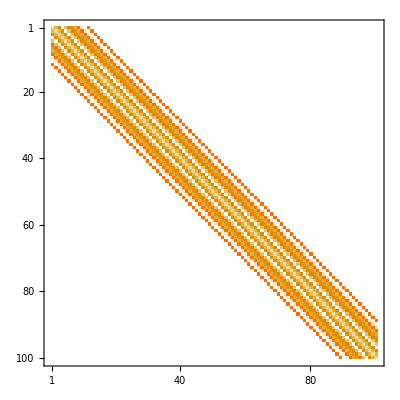

```mathematica
max=100000;
min=1;
sz=100;
bandsz=10;
data={{i_,i_}->RandomReal[{max,min}]};
func[k_]:={i_,j_}/;Abs[i-j]==k->RandomReal[{max,min}]
vec=Table[func[RandomInteger[]+k],{k,0,bandsz}];
AppendTo[data,vec];
data=Flatten[data];
s=SparseArray[data,{sz,sz}];
MatrixForm[s];
MatrixPlot[s]
```

```mathematica
matrices={Array[Style[Subscript[a,#1,#2],Red,Bold,16]&,{2,3}],Array[Style[Subscript[b,#1,#2],Blue,Bold,16]&,{3,2}],Array[Style[Subscript[c,#1,#2],Green,Bold,16]&,{2,2}],Array[Style[Subscript[d,#1,#2],Orange,Bold,16]&,{3,3}]};
MatrixForm/@matrices

SparseArray[Band[{1,3}]->matrices]//Normal//MatrixForm
```

{(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)),(b_(1,1) | b_(1,2)
b_(2,1) | b_(2,2)
b_(3,1) | b_(3,2)),(10_(1,1) | 10_(1,2)
10_(2,1) | 10_(2,2)),(d_(1,1) | d_(1,2) | d_(1,3)
d_(2,1) | d_(2,2) | d_(2,3)
d_(3,1) | d_(3,2) | d_(3,3))}

(0 | 0 | a_(1,1) | a_(1,2) | a_(1,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a_(2,1) | a_(2,2) | a_(2,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | b_(1,1) | b_(1,2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | b_(2,1) | b_(2,2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | b_(3,1) | b_(3,2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10_(1,1) | 10_(1,2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10_(2,1) | 10_(2,2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d_(1,1) | d_(1,2) | d_(1,3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d_(2,1) | d_(2,2) | d_(2,3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | d_(3,1) | d_(3,2) | d_(3,3))